# MA2330

## Chapter 1 : Linear Equations in Linear Algebra

### 1.1 Systems of Linear Equations.

#### Small Example

A linear system looks like this 
	4 x_1 | + | 3 x_2 | - | x_3 | = | 1
-2 x_1 | + | x_2 |   |   | = | 2
0.5 x_1 |   |   | + | X_3 | = | -2
It will not always be lined up as neatly!

The variables are x_1,x_2, and x_3.

Not all variables in the real world are called x_i

The coefficient matrix is A=(4 | 3 | -1
-2 | 1 | 0
0.5 | 0 | 1)

The coefficients of the first equation are 4,3,-1 etc.

Coefficients in most real world problems are real numbers (which our book writes as ℝ)

Most of our hand examples will have integers!

The right hand side (RHS) vector is b=(1
2
-2)

In fancy terminology we have ∑_(j=1)^3 a_(i,j)x_j=b_i  for i=1,2, and 3 which we are going to learn to write as A x = b

For i=1 we have a_(1,1)x_1+a_(1,2)x_2+a_(1,3)x_3=b_1

The matrix A∈ℝ^(3 × 3), the RHS b∈ℝ^3, and our task would be to compute x∈ℝ^3.

To save ourselves from copying variables the first thing we will always do is write down the matrix.

We will almost always call our variables x and our matrices A. When we are solving A x=b we will write down the augmented matrix by sticking the right hand side b on the back of A. The augmented matrix is written (A | | | b)

In this example (A | | | b)=(4 | 3 | -1 | 1
-2 | 1 | 0 | 2
0.5 | 0 | 1 | -2)∈ℝ^(3 × 4)

You get the matrix by lining up the terms carefully and then you neglect to write down the variables.

#### Nonlinear Terms

Any term involving the product of variables or any non-trivial function (Sine, Cosine, Log, Exp, ...) is nonlinear.   For example, x_1 x_2 is non-linear as is sin(x_3).

All the terms in all our equations need to be linear it is in the course name!

#### Geometry

Any linear equation in ℝ^2 defines a line. A set of two linear equations defines two lines in ℝ^2.

Nonparallel lines intersect in a single point.

Parallel lines never intersect.

Unless they lie right on top of each other.

Nearly parallel lines intersect but the intersection point is twitchy.

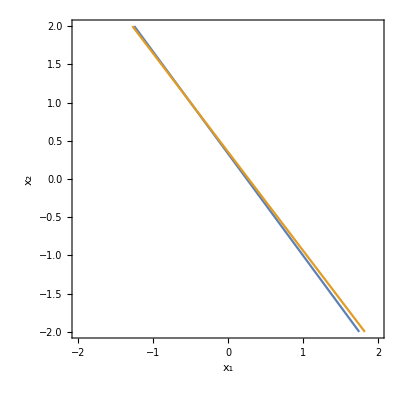

```mathematica
a1={4,3};b1=1;
a2={4,3.1};b2 =1.1;
ContourPlot[ {
a1.{x1,x2}==b1,
a2.{x1,x2}==b2
},
{x1,-2,2},{x2,-2,2},
AxesLabel->{"x_1","x_2"}]
```

Any linear equation in ℝ^3 defines a plane. A set of three linear equations defines three planes in ℝ^3

Three planes usually intersect in a single point.

Some degenerate sets of planes can fail to intersect.

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3={0.5,0,1};b3=-2;
ContourPlot3D[ {
a1.{x1,x2,x3}==b1,
a2.{x1,x2,x3}==b2,
a3.{x1,x2,x3}==b3
},
{x1,-2,2},{x2,-2,2},{x3,-2,2},
AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

Here is a degenerate set of planes.  We made a degenerate set by adding a_1 to a_2 to define a_3.  This set of three equations has no solution!

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3={2,4,-1};b3=-2;
ContourPlot3D[ {
a1.{x1,x2,x3}==b1,
a2.{x1,x2,x3}==b2,
a3.{x1,x2,x3}==b3
},
{x1,-12,12},{x2,-12,12},{x3,-12,12},
AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

Here is a degenerate set of planes with lots of solutions.  This degenerate set adds a_1 to a_2 to define a_3 and b_1 to b_2 to get b_3.

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3=a1+a2;b3=b1+b2;
ContourPlot3D[ {
a1.{x1,x2,x3}==b1,
a2.{x1,x2,x3}==b2,
a3.{x1,x2,x3}==b3
},
{x1,-12,12},{x2,-12,12},{x3,-12,12},
AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

#### Solving Equations by Hand

To solve a set of linear equations you simply eliminate variables by artfully combing equations.  It is good to be organized when you do this to avoid going in circles. We are going to do this on the board with the variables and show the matching operations on the augmented matrix

The operations on the augmented matrix are three types of elementary row operations

Replace one row by the sum of itself and a multiple of another row.

Interchange two rows.

Scale all entries in a row by a non-zero constant.

#### Solving Equations by Computer: Small Systems

All technical computational tools can solve linear systems.

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3={0.5,0,1};b3=-2;
Solve[ 
{a1.{x1,x2,x3}==b1,a2.{x1,x2,x3}==b2,a3.{x1,x2,x3}==b3},
{x1,x2,x3}]
```

{{x1→-0.666667,x2→0.666667,x3→-1.66667}}

The matrix form is simpler.

```mathematica
A={{4,3,-1},{-2,1,0},{0.5,0,1}};b={1,2,-2};
LinearSolve[A,b]
```

{-0.666667,0.666667,-1.66667}

There is a RowReduce command that mimics what we do by hand.

```mathematica
AugAb={{4,3,-1,1},{-2,1,0,2},{0.5,0,1,-2}};
RRef=RowReduce[AugA];
MatrixForm[RRef]
```

(1 | 0. | 0. | -0.666667
0 | 1 | 0. | 0.666667
0 | 0 | 1 | -1.66667)

You can build the augmented matrix from A and b.

```mathematica
ArrayFlatten[{{A,{b}ᵀ}}]
```

{{4,3,-1,1},{-2,1,0,2},{0.5,0,1,-2}}

#### Definitions, Questions, and Answers

Matrices are row equivalent if you can go from one to the other using Elementary Row Ops.

Systems with row equivalent Augmented Matrices have the same solutions.

Does a system have a solution? In other words does a solution exist?

If a solution exists, is it the only one? In other words, is the solution unique?

#### Solving Equations by Computer: Larger Systems

The computer organizes the computation and can do much larger computations. Lets see what big is? Our only real problem is making big matrices: we do not want to type them.

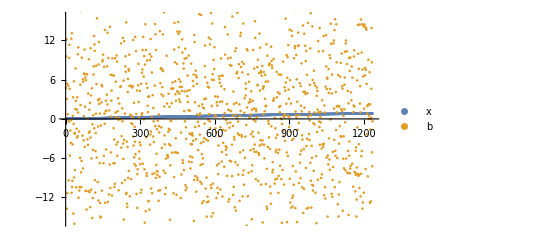

```mathematica
n=1234;
xIn=Table[ Sin[x],{x,0.0,1,1/n}];
A=RandomReal[{-1,1},{n+1,n+1}];
b=A.xIn;
Map[Dimensions,{A,xIn,b}] ;
ListPlot[{xIn,b},PlotLegends->{"x","b"}]
```

{0.03125,Null}

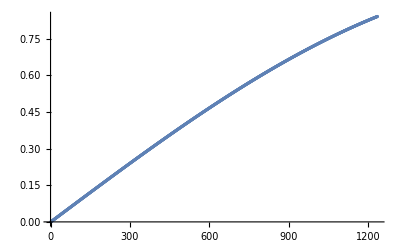

```mathematica
Timing[xOut=LinearSolve[A,b];]
ListPlot[xOut]
```

A good question is what will break first if we try to do larger computations?

#### Solving Equations by Computer: Real Matrices

What do real matrices look like.  A National Institute of Science and Technology (NIST) web page  https://math.nist.gov/MatrixMarket/ has a collection of real matrices.   Here is one

SparseArray[…]

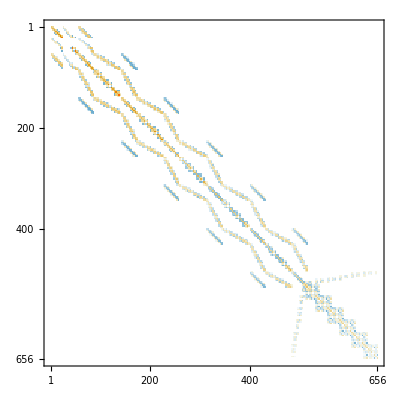

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/fidap/fidap021.mtx.gz"]
MatrixPlot[A]
```

Here is a larger matrix used in a LinearSolve.

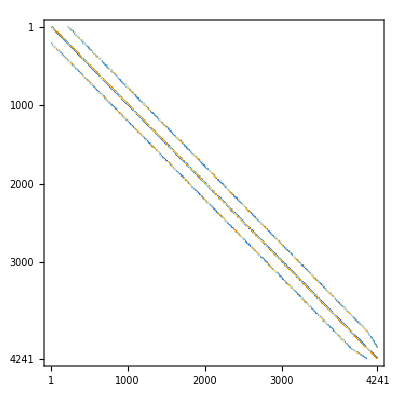

{0.03125,Null}

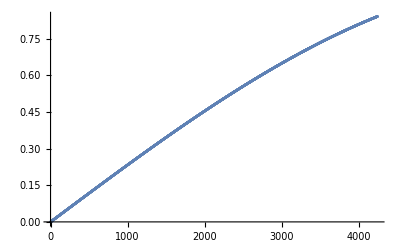

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/drivcav/e20r5000.mtx.gz"];
MatrixPlot[A]
n=Length[A];xIn=Table[ Sin[x],{x,0.0,1,1/(n-1)}];b=A.xIn;
Timing[xOut=LinearSolve[A,b];]
ListPlot[xOut]
```

#### Computational Examples

Ex2 (text)
2 | x_1 | + | -2 | x_2 | + | 1 | x_3 | = | 0
0 | x_1 | + | 2 | x_2 | + | -8 | x_3 | = | 8
5 | x_1 | + | 0 | x_2 | + | -5 | x_3 | = | 10→(1 | -2 | 1 | 0
0 | 2 | -8 | 8
5 | 0 | -5 | 10)~(1 | -2 | 1 | 0
0 | 1 | -4 | 4
0 | 0 | 1 | -1)→x_1 | = | 0-1 x_3+2 x_2
x_2 | = | 4+4 x_3
x_3 | = | -1

```mathematica
Map[RowReduce,{({{1, -2, 1, 0}, {0, 2, -8, 8}, {5, 0, -5, 10}}),({{1, -2, 1, 0}, {0, 1, -4, 4}, {0, 0, 1, -1}})}]
```

{{{1,0,0,1},{0,1,0,0},{0,0,1,-1}},{{1,0,0,1},{0,1,0,0},{0,0,1,-1}}}

Ex3 (text)
0 | x_1 | + | 1 | x_2 | + | -4 | x_3 | = | 8
2 | x_1 | + | -3 | x_2 | + | 2 | x_3 | = | 1
4 | x_1 | + | -8 | x_2 | + | 12 | x_3 | = | 1→(0 | 1 | -4 | 8
2 | -3 | 2 | 1
4 | -8 | 12 | 1)~(2 | -3 | 2 | 1
0 | 1 | -4 | 8
0 | 0 | 0 | 15)→2 x_1 | = | 1-2 x_3+3 x_2
x_2 | = | 8+4 x_3
x_3 | = | !!!
There is no such x_3.  So there is no solution to the original system.

```mathematica
Map[RowReduce,{({{0, 1, -4, 8}, {2, -3, 2, 1}, {4, -8, 12, 1}}),({{2, -3, 2, 1}, {0, 1, -4, 8}, {0, 0, 0, 15}})}]
```

{{{1,0,-5,0},{0,1,-4,0},{0,0,0,1}},{{1,0,-5,0},{0,1,-4,0},{0,0,0,1}}}

Ex3.5 
Suppose you had the same matrix but a different right hand side and you got
0 | x_1 | + | 1 | x_2 | + | -4 | x_3 | = | 8
2 | x_1 | + | -3 | x_2 | + | 2 | x_3 | = | 1
4 | x_1 | + | -8 | x_2 | + | 12 | x_3 | = | ?→(0 | 1 | -4 | 8
2 | -3 | 2 | 1
4 | -8 | 12 | ?)~(2 | -3 | 2 | 1
0 | 1 | -4 | 8
0 | 0 | 0 | 0)→2 x_1 | = | 1-2 x_3+3 x_2
x_2 | = | 8+4 x_3
0 x_3 | = | 0
Any x_3 works! So there are lots of solutions!!